## Damped Pendulum — Phase Space

## Done in class, February 11, 2025

This is the sixth notebook for you to finish in-class.

### Forced Oscillation

#### Force and Acceleration

```mathematica
gravity = 9.8; (* the value of gravity in units of meters / second-squared *)
length=0.25; (* a small, pendulum whose natural period is about one second *)
(* I happen to know the formula for the natural frequency and period of such *)
(* a pendulum, if you do not swing it too wildly. It is: *)
omega0=Sqrt[gravity/length];
period = 2Pi/omega0
beta=0.03; (* A real pendulum swinging in air has a small beta. *)
(* Note that the units of beta are frequency (aka inverse time). *)
omega3=Sqrt[omega0^2-beta^2];
a[t_, theta_, omega_]:=-gravity/length Sin[theta]-2 beta omega
```

1.00354

#### Simulation Parameters

```mathematica
tInitial = 0.0;
tFinal = 50.0; 
steps =200000;
deltaT = (tFinal - tInitial)/steps;
```

#### Initial Angle and Angular Velocity

Let’s let the pendulum be initially held still at 10 degrees and gently released:

```mathematica
thetaInitial=10 Degree;
omegaInitial=0.0;
initialConditions={tInitial,thetaInitial,omegaInitial};
```

#### General Second-Order Runge-Kutta — Implementation

The implementation will be almost the same as in the damped oscillation notebook you completed on Friday.

There are two small things have to be changed. Figure out what they are and then if you still have that code handy, you can almost completely re-use what you did in that notebook. Or just write it out again. The more times you write it out, the better you will remember it.

```mathematica
alpha=1;
rungeKutta2[cc_]:=(
(* Extract time, theta, and omega from the list *)
curTime=cc[[1]];
curTheta=cc[[2]];
curOmega=cc[[3]];
(* Compute tStar, thetaStar, and omegaStar *)
tStar = curTime + alpha deltaT;
thetaStar = curTheta + curOmega alpha deltaT;
omegaStar = curOmega + a[curTime,curTheta,curOmega];
(* General Second-Order Runge-Kutta *)
newTime=curTime+deltaT;
newOmega=curOmega+((1-1/(2alpha))a[curTime,curTheta,curOmega]+1/(2alpha)a[tStar,thetaStar,omegaStar])deltaT;
newTheta=curTheta+(curOmega+newOmega)deltaT/2;
(* Return the new values *)
{newTime, newTheta, newOmega}
)
(* Throw in a test of the function we just wrote *)
rungeKutta2[initialConditions]
(* The correct answer is {0.005, 0.174492,-0.016507}*)
```

{0.00025,0.174533,-0.0016507}

#### Displaying Oscillation

Nest the procedure, transpose the results, and produce a plot of the angle θ as a function of time:

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];rk2ResultsTransposed=Transpose[rk2Results];
times = rk2ResultsTransposed[[1]];
thetas = rk2ResultsTransposed[[2]];
thetaPlot = ListPlot[Transpose[{times,thetas}]];
(* the theoretical solution is approximately known, provided the angle remains small *)
(* let's plot the envelope of the theoretical solution *)
envelopeFunction[t_]:=thetaInitial Exp[-beta t]
approximateTheoreticalEnvelope=Plot[{envelopeFunction[t],-envelopeFunction[t]},{t, tInitial, tFinal}];
Show[{thetaPlot,approximateTheoreticalEnvelope}]
```

-Graphics-

In the preceding plot, the theoretical solution is approximately known, provided the angle remains small, and so I added the envelope of the theoretical solution to the plot. In the following plot, I have included the theoretical oscillation, not just the envelope (but the same approximation just mentioned still applies):

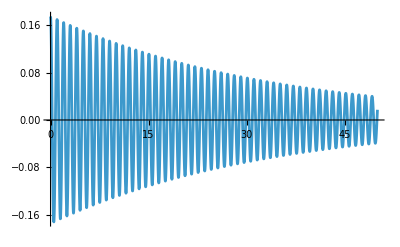

```mathematica
Plot[envelopeFunction[t]Cos[omega3 t],{t, tInitial, tFinal}]
```

It’s also nice to have an animation, arranged so that the default duration of the animation is the actual duration of the animation:

```mathematica
Animate[NumberLinePlot[thetas[[step]],PlotRange->{-20 Degree,20 Degree}],{step, 0, steps, 1}, DefaultDuration->tFinal-tInitial]
```

Wouldn’t it be even nicer to have our animation look like an actual pendulum?

#### Epilog — Phase Space